```mathematica
<<KerrGeodesics`
```

```mathematica
E0[a_,p_]:=Evaluate[KerrGeoEnergy[a,p,0,1]]
```

```mathematica
Ω[a_,p_]:=Evaluate["Ω_ϕ"/.KerrGeoFrequencies[a,p,0,1]]
```

```mathematica
p[a_,Ω_]:=Evaluate[First[SolveValues[Ω[a,p]==Ω,p]]];
```

```mathematica
dE0dΩ[a_,p_]:=Evaluate[Simplify[D[E0[a,p],p]/D[Ω[a,p],p]]]
```

```mathematica
dE0dΩLinear[a_,p_]:=Evaluate[Normal[Series[dE0dΩ[a,p],{a,0,1}]]]
```

```mathematica
dataDir=FileNameJoin[{"/Users/barry/Repositories/WaSABI/InspiralModels", "sf_data","1SF_Flux"}]
```

/Users/barry/Repositories/WaSABI/InspiralModels/sf_data/1SF_Flux

```mathematica
fluxdata1SF=Get[FileNameJoin[{dataDir,"Kerr_Circ","SMRfluxdata2025_36x36.data"}]];
```

```mathematica
rISCO[χ1_]:=3+Sqrt[3 χ1^2+(1+(1-χ1^2)^(1/3) ((1-χ1)^(1/3)+(1+χ1)^(1/3)))^2]-Sign[χ1] √((2-(1-χ1^2)^(1/3) ((1-χ1)^(1/3)+(1+χ1)^(1/3))) (4+(1-χ1^2)^(1/3) ((1-χ1)^(1/3)+(1+χ1)^(1/3))+2 Sqrt[3 χ1^2+(1+(1-χ1^2)^(1/3) ((1-χ1)^(1/3)+(1+χ1)^(1/3)))^2]));
```

```mathematica
ℱℐint1SFKerr = Interpolation[Table[{{Log[1-fluxdata1SF[[i]]["a"]], Sqrt[rISCO[fluxdata1SF[[i]]["a"]]/fluxdata1SF[[i]]["r"]]},N[fluxdata1SF[[i]]["r"]^5 fluxdata1SF[[i]]["inf"]["Value"]]},{i,1,Length[fluxdata1SF]}],Method->"Hermite",InterpolationOrder->{All,All}];
```

```mathematica
ℱℋint1SFKerr = Interpolation[Table[{{Log[1-fluxdata1SF[[i]]["a"]], Sqrt[rISCO[fluxdata1SF[[i]]["a"]]/fluxdata1SF[[i]]["r"]]},N[fluxdata1SF[[i]]["r"]^(15/2) fluxdata1SF[[i]]["hor"]["Value"]]},{i,1,Length[fluxdata1SF]}],Method->"Hermite",InterpolationOrder->{All,All}];
```

```mathematica
ℱKerr[a_,p_]:=Module[{χ1=a,ω=1/(a+p^(3/2))},ℱℐint1SFKerr[Log[1-χ1],Sqrt[rISCO[χ1]/(-χ1+1/ω)^(2/3)]] (ω/(1-χ1 ω))^(10/3)+ℱℋint1SFKerr[Log[1-χ1],Sqrt[rISCO[χ1]/(-χ1+1/ω)^(2/3)]] ω^5/(1-χ1 ω)^5]
```

```mathematica
ℱSchw[p_]:=ℱKerr[0,p];
```

```mathematica
{amin,amax}=MinMax[fluxdata1SF[[All,"a"]]]
```

{-0.99345000037950328593538597811494925504561013279562640891554216005376115785605681064154337637790419,0.99796390114032518371715537295389520378644361909354834633123951052003163465549765153291570772955231215}

```mathematica
{pmin,pmax}=MinMax[fluxdata1SF[[All,"r"]]]
```

{1.23980253542551930881947600612075867674887060013216743310059277288378418674461651638686580827732656,3.96588991183298911143306699801671854696857625760893885554668036702854175557982372096001434108961×10^7}

```mathematica
ℱKerrLinearℋ=Interpolation[Get[FileNameJoin[{dataDir,"Linear_Kerr_Circ","Slow_chi1_2SFCircSchwarzDotEHorizon.m"}]],InterpolationOrder->8];
```

```mathematica
ℱKerrLinearℐ=Interpolation[Get[FileNameJoin[{dataDir,"Linear_Kerr_Circ","Slow_chi1_2SFCircSchwarzDotEInf.m"}]],InterpolationOrder->8];
```

```mathematica
ℱKerrLinear[a_,p_]:=ℱSchw[p]+a(ℱKerrLinearℋ[p]+ℱKerrLinearℐ[p]);
```

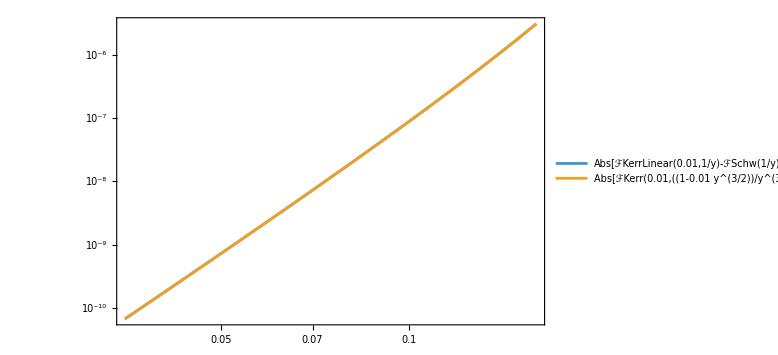

```mathematica
With[{a=0.01},LogLogPlot[{Abs[ℱKerrLinear[a,1/y]-ℱSchw[1/y]],Abs[(ℱKerr[a,((1-a y^(3/2))/y^(3/2))^(2/3)]-ℱSchw[1/y])]},{y,0.035,0.16},PlotTheme->"Detailed",ImageSize->Large]]
```

```mathematica
Plot3D[Log10[Abs[ℱKerr[a,((1-a p^(-3/2))/p^(-3/2))^(2/3)]/dE0dΩ[a,((1-a p^(-3/2))/p^(-3/2))^(2/3)]-ℱKerrLinear[a,p]/dE0dΩLinear[a,p]]],{a,amin,amax},{p,10,15}]
```

-Graphics3D-

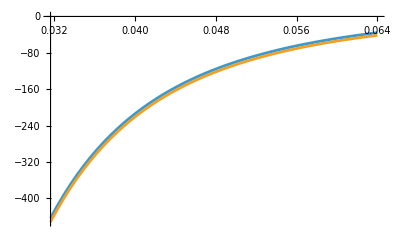

```mathematica
With[{a=0.3},Plot[{Ω0/(ℱKerr[a,((1-a Ω0)/Ω0)^(2/3)]/dE0dΩ[a,((1-a Ω0)/Ω0)^(2/3)]),Ω0/(ℱKerrLinear[a,Ω0^(-2/3)]/dE0dΩLinear[a,Ω0^(-2/3)])},{Ω0,10^(-3/2),6.25^(-3/2)}]]
```

```mathematica
Δϕ[a_]:=NIntegrate[Ω0/(ℱKerr[a,((1-a Ω0)/Ω0)^(2/3)]/dE0dΩ[a,((1-a Ω0)/Ω0)^(2/3)])-Ω0/(ℱKerrLinear[a,Ω0^(-2/3)]/dE0dΩLinear[a,Ω0^(-2/3)]),{Ω0,15^(-3/2),6.25^(-3/2)}]
```

```mathematica
Monitor[Δϕdata=Table[{a,If[a==0,0,Δϕ[a]]},{a,-0.5,0.5,0.01}];,a]
```

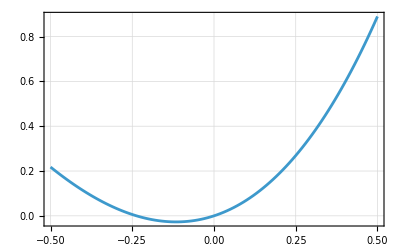

```mathematica
ListLinePlot[Δϕdata,PlotTheme->"Detailed"]
```

```mathematica
directory1SFSch = FileNameJoin[{"/Users/barry/Repositories/WaSABI/InspiralModels", "sf_data/1SF_Flux/Schwarz_Circ"}];
directory2SF = FileNameJoin[{"/Users/barry/Repositories/WaSABI/InspiralModels", "sf_data/2SF_Flux/Schwarz_Circ"}];
directory1SFLocalInvar = FileNameJoin[{"/Users/barry/Repositories/WaSABI/InspiralModels", "sf_data/1SF_Local_Invariants/Schwarz_Circ"}];
directorySecSpin = FileNameJoin[{"/Users/barry/Repositories/WaSABI/InspiralModels", "sf_data/Leading_S2_Flux/Schwarz_Circ"}];
directorystop=FileNameJoin[{"/Users/barry/Repositories/WaSABI/InspiralModels", "sf_data/stop_conditions"}];
directoryPrimarySpin = FileNameJoin[{"/Users/barry/Repositories/WaSABI/InspiralModels", "sf_data/1SF_Flux/Linear_Kerr_Circ"}];

fluxdata2SF=Get[FileNameJoin[{directory2SF, "2SFCircSchwarzDotEInf.m"}]];

fluxdata1SFSchwInf=Get[FileNameJoin[{directory1SFSch,"1SFCircSchwarzDotEInf.m"}]];
fluxdata1SFSchwHor=Get[FileNameJoin[{directory1SFSch,"1SFCircSchwarzDotEHorizon.m"}]];

spinfluxdataHor=Get[FileNameJoin[{directorySecSpin,"chi2_2SFCircSchwarzDotEHorizon.m"}]];
spinfluxdataInf=Get[FileNameJoin[{directorySecSpin,"chi2_2SFCircSchwarzDotEInf.m"}]];

slowspin1fluxdataHor=Get[FileNameJoin[{directoryPrimarySpin,"Slow_chi1_2SFCircSchwarzDotEHorizon.m"}]];
slowspin1fluxdataInf=Get[FileNameJoin[{directoryPrimarySpin,"Slow_chi1_2SFCircSchwarzDotEInf.m"}]];

invardata=Get[FileNameJoin[{directory1SFLocalInvar,"1SFCircSchwarzRedshfit.m"}]];
Ωcritdata=Get[FileNameJoin[{directorystop,"Stop1PAT1R.m"}]];
```

```mathematica
ℱℰℐ = Interpolation[fluxdata1SFSchwInf,InterpolationOrder->8];
ℱ2σℰℐ = Interpolation[spinfluxdataInf,InterpolationOrder->8];
ℱaℰℐ = Interpolation[slowspin1fluxdataInf,InterpolationOrder->8];
ℱ2ℰℐ := Function[{r0},Re[Exp[Interpolation[fluxdata2SF,InterpolationOrder->8][Log[r0]]]]];
```

```mathematica
ℱℰℋ = Interpolation[fluxdata1SFSchwHor,InterpolationOrder->8];
ℱ2σℰℋ = Interpolation[spinfluxdataHor,InterpolationOrder->8];
ℱaℰℋ = Interpolation[slowspin1fluxdataHor,InterpolationOrder->8];
```

```mathematica
z = Interpolation[invardata, InterpolationOrder->8];
```

```mathematica
ℱ1[r0_]:=ℱℰℐ[r0]+ℱℰℋ[r0];
ℱℒℋ[r0_]:=r0^(3/2) ℱℰℋ[r0];
ℱℒℐ[r0_]:=r0^(3/2) ℱℰℐ[r0];
ℒ1[r0_]:=ℱℒℋ[r0]+ℱℒℐ[r0];

ℱσ[r0_]:=ℱ2σℰℐ[r0]+ℱ2σℰℋ[r0];
ℱa[r0_]:=ℱaℰℋ[r0]+ℱaℰℐ[r0];

Eδm[y_]:=-(y/3) (1-6y)/(1-3y)^(3/2);
EFLx[x_]:=(1/2 z[x]-x/3z'[x]-1+Sqrt[1-3x]+x/6  (7-24x)/(1-3x)^(3/2));

dEdΩ[r0_,ν_,at1_,at2_,δm1_]:=Module[{M=1,x,dxdΩ},
 x=M/r0;
dxdΩ=(2 M)/(3 Sqrt[x]);
((M^2) (-1+6 x) )/(3 (1-3 x)^(3/2) Sqrt[x])+ ((at2 M^2 x (-5+12 x))/(3 ((1-3 x)^(3/2)) )-(2 at1 M^2 x (10-33 x+36 x^2))/(9 ((1-3 x)^(5/2)) )+ν( EFLx'[x]+δm1 Eδm'[x])dxdΩ)
];
dΩdttimesdEdΩ[r0_,ν_,at1_,at2_,δm1_]:=Module[{M=1,x,dxdΩ},
 x=M/r0;
-ν ℱ1[1/x]+ν^2 (-ℱ2ℰℐ[1/x]-δm1 (Sqrt[M/r0^3](-((2 r0^(5/2))/3))ℱ1'[r0] )-(at1 ℱa[1/x])/ν-(at2 ℱσ[1/x])/ν-(2 x^(5/2) (-2+3 x) ℱℒℋ[1/x])/(3 M (1-3 x)^(3/2))-Eδm[x] ℱℰℋ[1/x])];
```

```mathematica
dEdΩ0PA[r0_,ν_,at1_,at2_,δm1_]:=Module[{M=1,x,dxdΩ},
 x=M/r0;
dxdΩ=(2 M)/(3 Sqrt[x]);
((M^2) (-1+6 x) )/(3 (1-3 x)^(3/2) Sqrt[x])
];
dΩdttimesdEdΩ0PA[r0_,ν_,at1_,at2_,δm1_]:=Module[{M=1,x,dxdΩ},
 x=M/r0;
-ν ℱ1[1/x]];
```

```mathematica
Δϕ1PA[ν_]:=NIntegrate[Ω0/(dΩdttimesdEdΩ[Ω0^(-2/3),ν,0,0,0]/dEdΩ[Ω0^(-2/3),ν,0,0,0])-Ω0/(dΩdttimesdEdΩ0PA[Ω0^(-2/3),ν,0,0,0]/dEdΩ0PA[Ω0^(-2/3),ν,0,0,0]),{Ω0,Ω[0,15],Ω[0,6.25]}]
```

```mathematica
Monitor[Δϕ1PAdata=Table[{ν,Δϕ1PA[ν]},{ν,0.001,0.25,0.001}];,{ν}]
```

```mathematica
Δϕ1PAlimit=Δϕ1PA[0.00000001]
```

12.8176

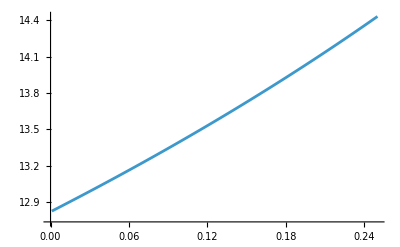

```mathematica
ListLinePlot[Δϕ1PAdata]
```

```mathematica
ListLinePlot[Δϕdata,PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
With[{m1=10^6,m2=10},{ν=(m1 m2)/(m1+m2)^2,ϵ=m2/m1},a/ϵ/.FindRoot[(Interpolation[Δϕdata][a])/ϵ==Δϕ1PAlimit,{a,0}]]//N
```

26.7918

```mathematica
With[{m1=10^6,m2=10},{ν=(m1 m2)/(m1+m2)^2,ϵ=m2/m1},a/ϵ/.FindRoot[Abs[(Interpolation[Δϕdata][a])/ϵ]==Δϕ1PAlimit,{a,-.001}]]//N
```

-26.8579

Conclusion: the 1PAT1R model is good provided a ≲ 26.8 m_1/m_2